{{0.2375,0.592021},{0.285,0.664876},{0.3325,0.790413},{0.38,0.923439},{0.4275,0.992265}}

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.051267 | 0.0483689 | 1.05992 | 0.366962
x | 2.1181 | 0.13546 | 15.6364 | 0.000568467

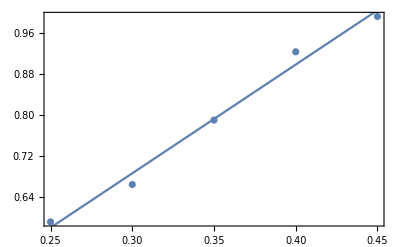

```mathematica
data={{0.25,0.5920209683800329},{0.30,0.664875805881917},{0.35,0.7904133319594417},{0.40,0.9234391064171161},{0.45,0.9922649303937388}};
corr[{x_,y_}]={x-x*0.05,y};
Map[corr,data]
lm=LinearModelFit[data,x,x];
lm["ParameterTable"]
Show[ListPlot[data],Plot[lm[x],{x,0,5}],Frame->True]
Export["konz",data,"Table"]
```